```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"CT-Knee_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

(* nucleon 0.1 0.3 0.6 vortex 0.4 0.3 0.3 *)
targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
iterationcount1=50;
iterationcount2=10;
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(* x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient,direction}
],{iterator,iterationcount1}];
```

154.019831

44

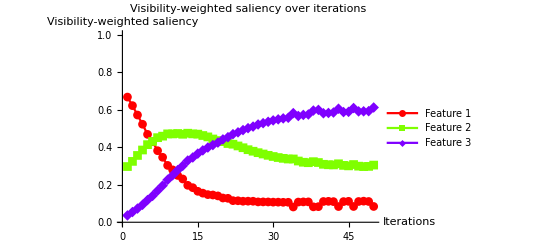

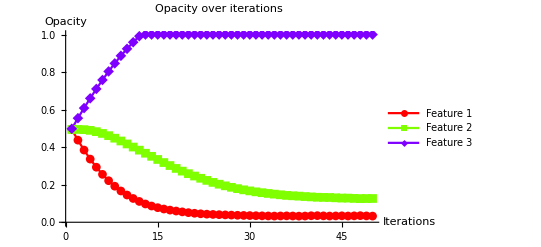

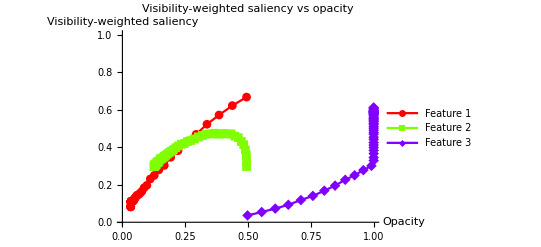

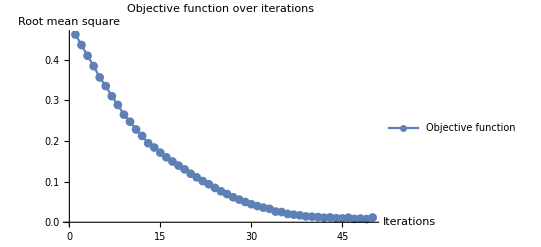

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps |  | 
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321979
0.0563686 | 1.13381
-0.00643958
-1.12737 | direction$323532
2 | 0.621306
0.324235
0.0544588 | 0.437427
0.49444
0.554408 | 0.435875 | -0.0528658
-0.00102095
0.0538868 | 1.04261
0.0484707
-1.09108 | 1.05732
0.0204189
-1.07774
3 | 0.571238
0.355895
0.072867 | 0.384561
0.493419
0.608295 | 0.409495 | -0.0480983
-0.00388308
0.0519814 | 0.942476
0.11179
-1.05427 | 0.961966
0.0776617
-1.03963
4 | 0.522069
0.384916
0.0930149 | 0.336463
0.489536
0.660276 | 0.384008 | -0.0432504
-0.00681752
0.0500679 | 0.844138
0.169832
-1.01397 | 0.865008
0.13635
-1.00136
5 | 0.468231
0.413437
0.118332 | 0.293213
0.482718
0.710344 | 0.356121 | -0.0380495
-0.00954984
0.0475994 | 0.736463
0.226874
-0.963337 | 0.760991
0.190997
-0.951988
6 | 0.429039
0.430451
0.14051 | 0.255163
0.473168
0.757943 | 0.334871 | -0.0338027
-0.0118234
0.045626 | 0.658077
0.260902
-0.91898 | 0.676054
0.236467
-0.912521
7 | 0.381134
0.450694
0.168171 | 0.22136
0.461345
0.803569 | 0.309958 | -0.0293489
-0.0135229
0.0428718 | 0.562269
0.301389
-0.863658 | 0.586978
0.270458
-0.857436
8 | 0.346135
0.458669
0.195196 | 0.192012
0.447822
0.846441 | 0.288459 | -0.0254238
-0.0149168
0.0403406 | 0.492271
0.317338
-0.809609 | 0.508476
0.298337
-0.806813
9 | 0.302875
0.470868
0.226257 | 0.166588
0.432905
0.886782 | 0.264599 | -0.021497
-0.015777
0.0372739 | 0.405751
0.341735
-0.747486 | 0.429939
0.31554
-0.745479
10 | 0.27912
0.47054
0.25034 | 0.145091
0.417128
0.924056 | 0.247272 | -0.0184561
-0.0164951
0.0349512 | 0.358239
0.341081
-0.69932 | 0.369121
0.329902
-0.699024
11 | 0.249485
0.472826
0.277689 | 0.126635
0.400633
0.959007 | 0.228107 | -0.015774
-0.0164826
0.0322567 | 0.298971
0.345651
-0.644622 | 0.315481
0.329652
-0.645133
12 | 0.230615
0.468772
0.300613 | 0.110861
0.38415
0.991263 | 0.212271 | -0.0135031
-0.0164677
0.0299708 | 0.26123
0.337543
-0.598773 | 0.270061
0.329354
-0.599415
13 | 0.196839
0.474343
0.328818 | 0.0973576
0.367683
1. | 0.194348 | -0.0108824
-0.0164162
0.0272986 | 0.193678
0.348686
-0.542365 | 0.217649
0.328323
-0.545972
14 | 0.184169
0.470799
0.345033 | 0.0864751
0.351267
1. | 0.183725 | -0.0087971
-0.0167741
0.0255712 | 0.168337
0.341597
-0.509935 | 0.175942
0.335483
-0.511425
15 | 0.164894
0.469461
0.365645 | 0.077678
0.334492
1. | 0.171124 | -0.0071915
-0.0164158
0.0236073 | 0.129787
0.338922
-0.468709 | 0.14383
0.328317
-0.472147
16 | 0.155003
0.462108
0.382888 | 0.0704865
0.318077
1. | 0.159627 | -0.00578692
-0.0160035
0.0217904 | 0.110007
0.324217
-0.434224 | 0.115738
0.320069
-0.435808
17 | 0.147212
0.45478
0.398008 | 0.0646996
0.302073
1. | 0.149429 | -0.00494239
-0.0153224
0.0202648 | 0.0944236
0.309561
-0.403984 | 0.0988477
0.306449
-0.405297
18 | 0.145199
0.443606
0.411196 | 0.0597572
0.286751
1. | 0.139418 | -0.00446041
-0.0144023
0.0188627 | 0.0903971
0.287211
-0.377608 | 0.0892082
0.288046
-0.377255
19 | 0.140351
0.435195
0.424454 | 0.0552968
0.272348
1. | 0.130029 | -0.00412848
-0.0134544
0.0175829 | 0.0807025
0.27039
-0.351092 | 0.0825696
0.269088
-0.351658
20 | 0.129151
0.42942
0.441429 | 0.0511683
0.258894
1. | 0.119365 | -0.00332749
-0.0126686
0.0159961 | 0.0583029
0.258839
-0.317142 | 0.0665497
0.253372
-0.319922
21 | 0.127511
0.419376
0.453112 | 0.0478408
0.246225
1. | 0.110429 | -0.00272297
-0.0119561
0.014679 | 0.0550227
0.238753
-0.293776 | 0.0544594
0.239121
-0.293581
22 | 0.11505
0.41573
0.46922 | 0.0451179
0.234269
1. | 0.101198 | -0.00203656
-0.0112498
0.0132864 | 0.0301003
0.23146
-0.26156 | 0.0407312
0.224996
-0.265727
23 | 0.114507
0.406483
0.47901 | 0.0430813
0.223019
1. | 0.09343 | -0.00141887
-0.0106672
0.0120861 | 0.0290141
0.212965
-0.241979 | 0.0283775
0.213344
-0.241721
24 | 0.112011
0.397001
0.490988 | 0.0416624
0.212352
1. | 0.0845323 | -0.00125961
-0.00966562
0.0109252 | 0.0240215
0.194003
-0.218024 | 0.0251922
0.193312
-0.218505
25 | 0.112254
0.386495
0.501251 | 0.0404028
0.202687
1. | 0.0761202 | -0.00114974
-0.00869458
0.00984433 | 0.0245083
0.172989
-0.197498 | 0.0229949
0.173892
-0.196887
26 | 0.111877
0.378369
0.509755 | 0.0392531
0.193992
1. | 0.0693468 | -0.00115038
-0.00785939
0.00900977 | 0.0237537
0.156737
-0.180491 | 0.0230076
0.157188
-0.180195
27 | 0.108431
0.370678
0.520891 | 0.0381027
0.186133
1. | 0.0614403 | -0.000954059
-0.00700234
0.0079564 | 0.0168611
0.141357
-0.158218 | 0.0190812
0.140047
-0.159128
28 | 0.10847
0.363619
0.527911 | 0.0371486
0.17913
1. | 0.0557253 | -0.000803825
-0.00638742
0.00719125 | 0.0169401
0.127238
-0.144178 | 0.0160765
0.127748
-0.143825
29 | 0.108161
0.356532
0.535307 | 0.0363448
0.172743
1. | 0.0498253 | -0.000785057
-0.00567181
0.00645686 | 0.0163211
0.113065
-0.129386 | 0.0157011
0.113436
-0.129137
30 | 0.107124
0.350329
0.542547 | 0.0355597
0.167071
1. | 0.0442889 | -0.000719268
-0.00502875
0.00574801 | 0.0142479
0.100657
-0.114905 | 0.0143854
0.100575
-0.11496
31 | 0.107071
0.344765
0.548164 | 0.0348405
0.162042
1. | 0.0397526 | -0.000671429
-0.00449812
0.00516955 | 0.0141412
0.0895299
-0.103671 | 0.0134286
0.0899624
-0.103391
32 | 0.106264
0.340458
0.553278 | 0.034169
0.157544
1. | 0.0358658 | -0.000632437
-0.00404214
0.00467458 | 0.0125271
0.0809169
-0.0934439 | 0.0126487
0.0808429
-0.0934916
33 | 0.106403
0.336899
0.556698 | 0.0335366
0.153502
1. | 0.0330532 | -0.000607487
-0.00371009
0.00431758 | 0.0128057
0.0737974
-0.0866031 | 0.0121497
0.0742019
-0.0863516
34 | 0.0813833
0.337197
0.58142 | 0.0329291
0.149792
1. | 0.0263022 | 0.00057182
-0.00346897
0.00289715 | -0.0372333
0.0743939
-0.0371605 | -0.0114364
0.0693794
-0.057943
35 | 0.107555
0.326253
0.566192 | 0.0335009
0.146323
1. | 0.0250949 | 0.000579115
-0.00332184
0.00274273 | 0.0151103
0.0525054
-0.0676157 | -0.0115823
0.0664368
-0.0548545
36 | 0.108502
0.319669
0.571829 | 0.0340801
0.143001
1. | 0.0204348 | -0.000721327
-0.00206287
0.0027842 | 0.0170045
0.0393374
-0.0563419 | 0.0144265
0.0412574
-0.0556839
37 | 0.108599
0.317259
0.574142 | 0.0333587
0.140938
1. | 0.0186233 | -0.00081554
-0.00176101
0.00257655 | 0.0171987
0.0345182
-0.0517169 | 0.0163108
0.0352201
-0.0515309
38 | 0.0821202
0.322763
0.595117 | 0.0325432
0.139177
1. | 0.016948 | 0.000530916
-0.00228959
0.00175867 | -0.0357597
0.0455265
-0.00976684 | -0.0106183
0.0457918
-0.0351735
39 | 0.0830904
0.318203
0.598707 | 0.0330741
0.136888
1. | 0.0143637 | 0.00159988
-0.00188393
0.000284049 | -0.0338192
0.0364057
-0.00258647 | -0.0319977
0.0376787
-0.00568099
40 | 0.110563
0.308796
0.58064 | 0.034674
0.135004
1. | 0.0137084 | 0.000435749
-0.00185384
0.00141809 | 0.0211269
0.0175926
-0.0387194 | -0.00871497
0.0370768
-0.0283618
41 | 0.111408
0.306284
0.582308 | 0.0351097
0.13315
1. | 0.0126837 | -0.00105761
-0.000725887
0.0017835 | 0.0228162
0.0125675
-0.0353837 | 0.0211522
0.0145177
-0.03567
42 | 0.109921
0.305475
0.584604 | 0.0340521
0.132424
1. | 0.0110368 | -0.000992402
-0.000547121
0.00153952 | 0.0198417
0.0109502
-0.0307918 | 0.019848
0.0109424
-0.0307905
43 | 0.0836934
0.311487
0.60482 | 0.0330597
0.131877
1. | 0.0118474 | 0.000624453
-0.00165869
0.00103424 | -0.0326132
0.0229739
0.00963927 | -0.0124891
0.0331738
-0.0206847
44 | 0.110041
0.303021
0.586938 | 0.0336842
0.130218
1. | 0.00967077 | 0.000588819
-0.00136344
0.000774622 | 0.0200823
0.00604208
-0.0261244 | -0.0117764
0.0272688
-0.0154924
45 | 0.11145
0.300336
0.588213 | 0.034273
0.128855
1. | 0.00948951 | -0.00106963
-0.000167103
0.00123673 | 0.0229007
0.000672956
-0.0235736 | 0.0213925
0.00334206
-0.0247346
46 | 0.084024
0.307464
0.608512 | 0.0332034
0.128688
1. | 0.0113049 | 0.000923653
-0.00159194
0.000668283 | -0.031952
0.0149273
0.0170247 | -0.0184731
0.0318387
-0.0133657
47 | 0.110582
0.298765
0.590652 | 0.034127
0.127096
1. | 0.008183 | 0.000923065
-0.001066
0.000142939 | 0.0211643
-0.00246908
-0.0186952 | -0.0184613
0.0213201
-0.00285878
48 | 0.112356
0.296568
0.591076 | 0.0350501
0.12603
1. | 0.00902004 | -0.00120682
0.000245492
0.000961329 | 0.0247116
-0.006863
-0.0178486 | 0.0241364
-0.00490983
-0.0192266
49 | 0.110599
0.297606
0.591795 | 0.0338433
0.126275
1. | 0.00786128 | -0.00106937
0.000271373
0.000797997 | 0.0211982
-0.00478747
-0.0164108 | 0.0213874
-0.00542745
-0.0159599
50 | 0.0840685
0.304551
0.61138 | 0.0327739
0.126547
1. | 0.0116051 | 0.00163135
-0.000660128
-0.000971219 | -0.031863
0.00910299
0.02276 | -0.0326269
0.0132026
0.0194244

```mathematica
t2-t1
iteration
saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rmslist5=#3&@@@list;
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_newton.png",rms5];
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_newton.png",table5];
path5=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path5]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient}
],{iterator,iterationcount1}];
```

164.1645

47

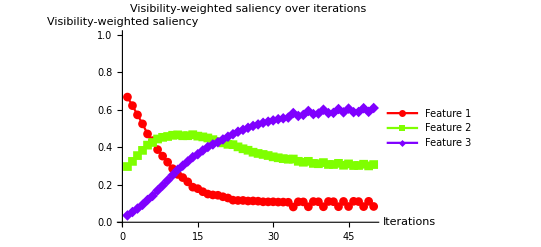

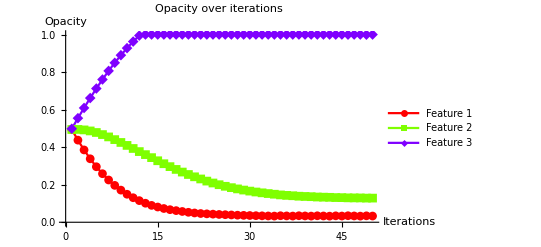

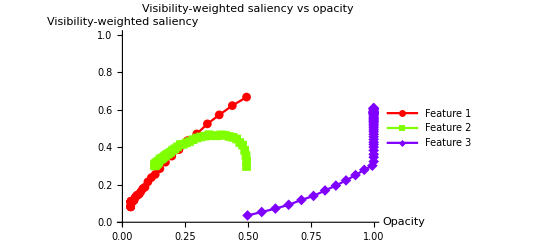

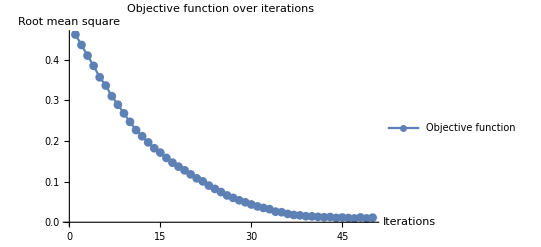

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321979
0.0563686 | 1.13381
-0.00643958
-1.12737
2 | 0.621306
0.324235
0.0544588 | 0.437427
0.49444
0.554408 | 0.435875 | -0.0521306
-0.00242354
0.0545541 | 1.04261
0.0484707
-1.09108
3 | 0.572025
0.355156
0.0728191 | 0.385297
0.492016
0.608962 | 0.409784 | -0.0472025
-0.00551561
0.0527181 | 0.944049
0.110312
-1.05436
4 | 0.524111
0.382874
0.0930151 | 0.338094
0.4865
0.66168 | 0.384609 | -0.0424111
-0.00828736
0.0506985 | 0.848223
0.165747
-1.01397
5 | 0.470485
0.410824
0.118691 | 0.295683
0.478213
0.712378 | 0.356464 | -0.0370485
-0.0110824
0.0481309 | 0.740969
0.221648
-0.962617
6 | 0.434818
0.424917
0.140265 | 0.258634
0.467131
0.760509 | 0.336186 | -0.0334818
-0.0124917
0.0459735 | 0.669635
0.249835
-0.91947
7 | 0.387039
0.44355
0.169411 | 0.225153
0.454639
0.806483 | 0.310056 | -0.0287039
-0.014355
0.0430589 | 0.574077
0.2871
-0.861178
8 | 0.352278
0.452337
0.195385 | 0.196449
0.440284
0.849542 | 0.289001 | -0.0252278
-0.0152337
0.0404615 | 0.504556
0.304675
-0.809231
9 | 0.320053
0.456906
0.22304 | 0.171221
0.42505
0.890003 | 0.267794 | -0.0220053
-0.0156906
0.037696 | 0.440106
0.313813
-0.753919
10 | 0.285424
0.463384
0.251192 | 0.149216
0.40936
0.927699 | 0.246809 | -0.0185424
-0.0163384
0.0348808 | 0.370848
0.326769
-0.697616
11 | 0.254941
0.465525
0.279534 | 0.130673
0.393021
0.96258 | 0.226645 | -0.0154941
-0.0165525
0.0320466 | 0.309883
0.33105
-0.640932
12 | 0.237983
0.46088
0.301137 | 0.115179
0.376469
0.994627 | 0.211534 | -0.0137983
-0.016088
0.0298863 | 0.275965
0.32176
-0.597725
13 | 0.215277
0.461064
0.323659 | 0.101381
0.360381
1. | 0.196295 | -0.0115277
-0.0161064
0.0276341 | 0.230554
0.322128
-0.552682
14 | 0.187
0.466298
0.346702 | 0.0898533
0.344274
1. | 0.182011 | -0.00869995
-0.0166298
0.0253298 | 0.173999
0.332597
-0.506596
15 | 0.178882
0.458801
0.362317 | 0.0811533
0.327644
1. | 0.171205 | -0.00788823
-0.0158801
0.0237683 | 0.157765
0.317602
-0.475367
16 | 0.162669
0.454653
0.382677 | 0.0732651
0.311764
1. | 0.158192 | -0.00626694
-0.0154653
0.0217323 | 0.125339
0.309307
-0.434646
17 | 0.15024
0.448937
0.400823 | 0.0669981
0.296299
1. | 0.14649 | -0.00502397
-0.0148937
0.0199177 | 0.100479
0.297874
-0.398353
18 | 0.145474
0.440005
0.414521 | 0.0619742
0.281405
1. | 0.136714 | -0.00454741
-0.0140005
0.0185479 | 0.0909482
0.28001
-0.370959
19 | 0.143788
0.429848
0.426365 | 0.0574268
0.267405
1. | 0.127707 | -0.00437875
-0.0129848
0.0173635 | 0.087575
0.259695
-0.34727
20 | 0.135819
0.422961
0.44122 | 0.053048
0.25442
1. | 0.117776 | -0.00358187
-0.0122961
0.015878 | 0.0716373
0.245922
-0.317559
21 | 0.129189
0.415185
0.455626 | 0.0494661
0.242124
1. | 0.107956 | -0.00291892
-0.0115185
0.0144374 | 0.0583785
0.23037
-0.288749
22 | 0.117616
0.413347
0.469037 | 0.0465472
0.230605
1. | 0.100514 | -0.00176163
-0.0113347
0.0130963 | 0.0352326
0.226694
-0.261926
23 | 0.116073
0.40159
0.482337 | 0.0447856
0.219271
1. | 0.0902284 | -0.0016073
-0.010159
0.0117663 | 0.0321461
0.20318
-0.235326
24 | 0.116151
0.391454
0.492395 | 0.0431783
0.209112
1. | 0.0820639 | -0.00161508
-0.00914539
0.0107605 | 0.0323016
0.182908
-0.215209
25 | 0.113177
0.383568
0.503255 | 0.0415632
0.199966
1. | 0.0741997 | -0.0013177
-0.00835678
0.00967448 | 0.026354
0.167136
-0.19349
26 | 0.113647
0.37308
0.513273 | 0.0402455
0.19161
1. | 0.0659506 | -0.00136467
-0.007308
0.00867267 | 0.0272934
0.14616
-0.173453
27 | 0.112281
0.366507
0.521212 | 0.0388808
0.184302
1. | 0.0599489 | -0.00122806
-0.00665074
0.0078788 | 0.0245612
0.133015
-0.157576
28 | 0.108981
0.361193
0.529826 | 0.0376528
0.177651
1. | 0.0540047 | -0.000898114
-0.00611925
0.00701737 | 0.0179623
0.122385
-0.140347
29 | 0.108617
0.355421
0.535962 | 0.0367547
0.171532
1. | 0.049148 | -0.000861653
-0.00554212
0.00640377 | 0.0172331
0.110842
-0.128075
30 | 0.108948
0.348517
0.542535 | 0.035893
0.165989
1. | 0.043727 | -0.000894829
-0.00485167
0.00574649 | 0.0178966
0.0970333
-0.11493
31 | 0.107464
0.343537
0.548999 | 0.0349982
0.161138
1. | 0.038954 | -0.000746373
-0.00435369
0.00510007 | 0.0149275
0.0870739
-0.102001
32 | 0.107375
0.338967
0.553658 | 0.0342518
0.156784
1. | 0.0352154 | -0.000737514
-0.00389668
0.00463419 | 0.0147503
0.0779335
-0.0926838
33 | 0.106538
0.335734
0.557728 | 0.0335143
0.152887
1. | 0.03218 | -0.000653803
-0.00357344
0.00422725 | 0.0130761
0.0714689
-0.0845449
34 | 0.081416
0.336775
0.581809 | 0.0328605
0.149314
1. | 0.0260043 | 0.0018584
-0.0036775
0.00181909 | -0.037168
0.0735499
-0.0363819
35 | 0.109042
0.324679
0.56628 | 0.0347189
0.145636
1. | 0.0246838 | -0.000904156
-0.00246789
0.00337205 | 0.0180831
0.0493579
-0.067441
36 | 0.108389
0.319753
0.571858 | 0.0338147
0.143169
1. | 0.0204333 | -0.000838932
-0.00197531
0.00281424 | 0.0167786
0.0395062
-0.0562849
37 | 0.0825279
0.324574
0.592898 | 0.0329758
0.141193
1. | 0.0178845 | 0.00174721
-0.00245736
0.00071015 | -0.0349443
0.0491473
-0.014203
38 | 0.11032
0.313533
0.576147 | 0.034723
0.138736
1. | 0.0169174 | -0.00103202
-0.00135326
0.00238528 | 0.0206404
0.0270652
-0.0477056
39 | 0.109213
0.311773
0.579014 | 0.033691
0.137383
1. | 0.0148759 | -0.000921288
-0.00117729
0.00209858 | 0.0184258
0.0235458
-0.0419715
40 | 0.0825772
0.317831
0.599592 | 0.0327697
0.136205
1. | 0.014395 | 0.00174228
-0.00178306
0.000040782 | -0.0348456
0.0356612
-0.000815639
41 | 0.110675
0.307892
0.581434 | 0.034512
0.134422
1. | 0.0131775 | -0.00106746
-0.000789171
0.00185663 | 0.0213493
0.0157834
-0.0371327
42 | 0.109555
0.307685
0.58276 | 0.0334445
0.133633
1. | 0.0122143 | -0.000955513
-0.000768471
0.00172398 | 0.0191103
0.0153694
-0.0344797
43 | 0.0829026
0.313822
0.603275 | 0.032489
0.132865
1. | 0.0128336 | 0.00170974
-0.00138222
-0.000327519 | -0.0341948
0.0276444
0.00655038
44 | 0.110852
0.303702
0.585446 | 0.0341987
0.131482
0.999672 | 0.0106974 | -0.00108525
-0.000370177
0.00145543 | 0.021705
0.00740355
-0.0291085
45 | 0.083736
0.310832
0.605432 | 0.0331135
0.131112
1. | 0.0117098 | 0.0016264
-0.00108323
-0.000543164 | -0.0325279
0.0216647
0.0108633
46 | 0.111486
0.302194
0.586321 | 0.0347399
0.130029
0.999457 | 0.0103899 | -0.00114856
-0.000219352
0.00136791 | 0.0229712
0.00438704
-0.0273582
47 | 0.110106
0.302401
0.587492 | 0.0335913
0.12981
1. | 0.00938692 | -0.00101062
-0.000240142
0.00125076 | 0.0202124
0.00480284
-0.0250152
48 | 0.0833239
0.309075
0.607601 | 0.0325807
0.129569
1. | 0.0118071 | 0.00166761
-0.000907534
-0.000760073 | -0.0333521
0.0181507
0.0152015
49 | 0.111452
0.300277
0.58827 | 0.0342483
0.128662
0.99924 | 0.00946611 | -0.00114524
-0.0000277434
0.00117298 | 0.0229047
0.000554867
-0.0234596
50 | 0.0840303
0.307331
0.608638 | 0.0331031
0.128634
1. | 0.0113049 | 0.00159697
-0.00073315
-0.000863824 | -0.0319395
0.014663
0.0172765

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_fixed.png",table1];
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

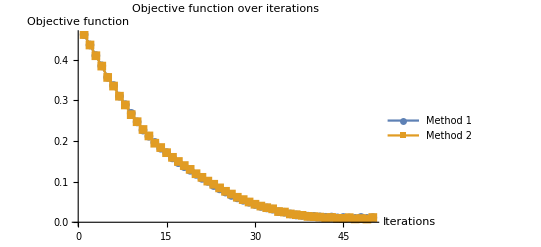

```mathematica
rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_newton.png",rmslists1];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

50.4495402

6

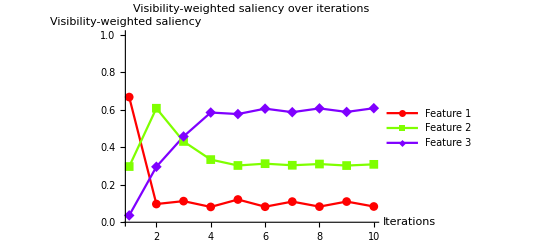

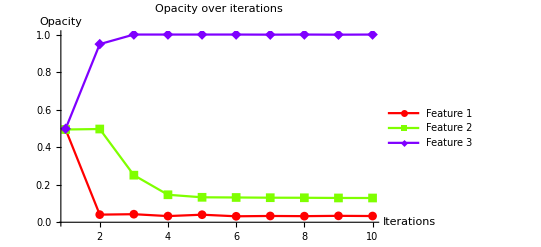

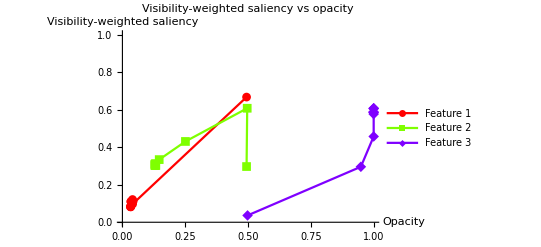

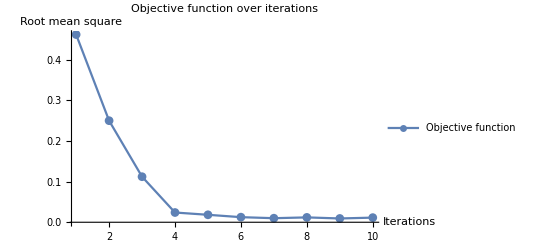

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321979
0.0563686 | 8
2 | 0.0971045
0.607334
0.295561 | 0.0405934
0.496693
0.948988 | 0.249764 | 0.000289548
-0.0307334
0.0304439 | 8
3 | 0.112551
0.430455
0.456995 | 0.0429098
0.250826
1. | 0.111992 | -0.00125509
-0.0130455
0.0143005 | 8
4 | 0.0816348
0.333807
0.584558 | 0.032869
0.146462
1. | 0.0239347 | 0.00183652
-0.00338067
0.00154415 | 4
5 | 0.12116
0.302399
0.576441 | 0.0402151
0.13294
1. | 0.0183353 | -0.00211601
-0.000239911
0.00235592 | 4
6 | 0.0827665
0.312073
0.605161 | 0.0317511
0.13198
1. | 0.0125083 | 0.00172335
-0.00120725
-0.000516099 | 1
7 | 0.109987
0.303606
0.586407 | 0.0334744
0.130773
0.999484 | 0.00995858 | -0.000998747
-0.000360556
0.0013593 | 1
8 | 0.0832406
0.310167
0.606592 | 0.0324757
0.130412
1. | 0.0119402 | 0.00167594
-0.0010167
-0.000659238 | 1
9 | 0.110241
0.302042
0.587718 | 0.0341516
0.129396
0.999341 | 0.00930767 | -0.00102407
-0.000204177
0.00122824 | 1
10 | 0.0839149
0.30848
0.607605 | 0.0331275
0.129191
1. | 0.0113795 | 0.00160851
-0.000848044
-0.000760465 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_parallelsearch.png",table2];
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,iterationcount2}];
```

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_linesearch.png",table3];
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

81.6202978

6

-Graphics-

-Graphics-

-Graphics-

-Graphics-

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.666905
0.29678
0.0363145 | 0.494118
0.494118
0.498039 | 0.461567 | -0.0566905
0.000321979
0.0563686 | 8
2 | 0.0971045
0.607334
0.295561 | 0.0405934
0.496693
0.948988 | 0.249764 | 0.000289548
-0.0307334
0.0304439 | 8
3 | 0.112551
0.430455
0.456995 | 0.0429098
0.250826
1. | 0.111992 | -0.00125509
-0.0130455
0.0143005 | 8
4 | 0.0816348
0.333807
0.584558 | 0.032869
0.146462
1. | 0.0239347 | 0.00183652
-0.00338067
0.00154415 | 4
5 | 0.12116
0.302399
0.576441 | 0.0402151
0.13294
1. | 0.0183353 | -0.00211601
-0.000239911
0.00235592 | 4
6 | 0.0827665
0.312073
0.605161 | 0.0317511
0.13198
1. | 0.0125083 | 0.00172335
-0.00120725
-0.000516099 | 1
7 | 0.109987
0.303606
0.586407 | 0.0334744
0.130773
0.999484 | 0.00995858 | -0.000998747
-0.000360556
0.0013593 | 1
8 | 0.0832406
0.310167
0.606592 | 0.0324757
0.130412
1. | 0.0119402 | 0.00167594
-0.0010167
-0.000659238 | 1
9 | 0.110241
0.302042
0.587718 | 0.0341516
0.129396
0.999341 | 0.00930767 | -0.00102407
-0.000204177
0.00122824 | 1
10 | 0.0839149
0.30848
0.607605 | 0.0331275
0.129191
1. | 0.0113795 | 0.00160851
-0.000848044
-0.000760465 | 1

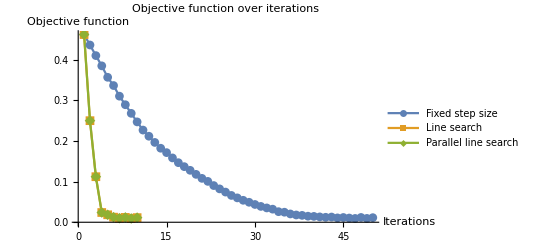

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Fixed step size","Line search","Parallel line search"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.png",rmslists2];
```

```mathematica
(*(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,70}];*)
```

```mathematica
(*t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];*)
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

CT-Knee_naive→{{154.019831,44,{0.0327739,0.126547,1.}},{164.1645,47,{0.0331031,0.128634,1.}},{50.4495402,6,{0.0331275,0.129191,1.}},{81.6202978,6,{0.0331275,0.129191,1.}}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[plotpath<>dataname<>"_parameterspace.png",sp];
Export[plotpath<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],plotpath<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-